```mathematica
h[ϕ_,θ_,p_,q_]:=1/2(q^2+p^2 Csc[θ]^2)+Cos[θ]+1;
```

{{ϕ→InterpolatingFunction[…],θ→InterpolatingFunction[…],pphi→InterpolatingFunction[…],ptheta→InterpolatingFunction[…]}}

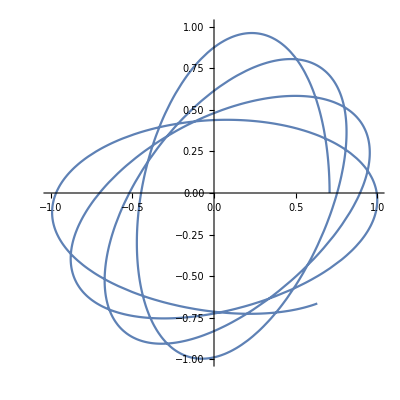

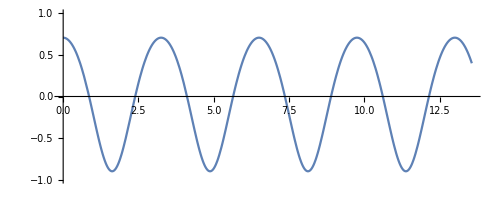

-Graphics3D-

```mathematica
Subscript[t, 0]=4π+1;

s=NDSolve[{
ϕ'[t]==pphi[t] Csc[θ[t]]^2,
θ'[t]==ptheta[t],
pphi'[t]==0,
ptheta'[t]==Sin[θ[t]]+pphi[t]^2 Cot[θ[t]] Csc[θ[t]]^2,
ϕ[0]==0,
θ[0]==π/4,
pphi[0]==1,
ptheta[0]==0
},{ϕ,θ,pphi,ptheta},{t,0,Subscript[t, 0]}]

ParametricPlot[Evaluate[{Cos[ϕ[t]]Sin[θ[t]],Sin[ϕ[t]]Sin[θ[t]]}/.s],{t,0,Subscript[t, 0]},PlotRange->{{-1,1},{-1,1}}]

ParametricPlot[Evaluate[{t,Cos[θ[t]]}/.s],{t,0,Subscript[t, 0]},PlotRange->{{0,Subscript[t, 0]},{-1,1}}]

ParametricPlot3D[Evaluate[{Cos[ϕ[t]]Sin[θ[t]],Sin[ϕ[t]]Sin[θ[t]],Cos[θ[t]]}/.s],{t,0,Subscript[t, 0]},PlotRange->{{-1,1},{-1,1}}]
```